```mathematica
Convolve[Exp[-x]UnitStep[x],Sin[x],x,y]
```

1/2 (-Cos[y]+Sin[y])

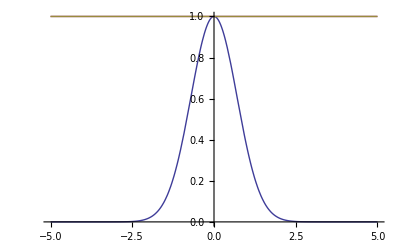

```mathematica
f[x_]:=Exp[-x^2];
g[x_,w_]:=UnitStep[x+w]-UnitStep[x-w]
(*Convolve[f[x],g[x],x,y]*)
h[x_,w_]:=(1/2 √π (1+Erf[w+x])-1/2 √π Erfc[w-x])/(1/2 √π (1+Erf[w])-1/2 √π Erfc[w])
w=8.0;
Plot[{f[m],g[m,w],h[m,w]},{m,-5,5},PlotRange->All]
```

```mathematica
h[p]
```

1/2 √π (1+Erf[1+p])-1/2 √π Erfc[1-p]

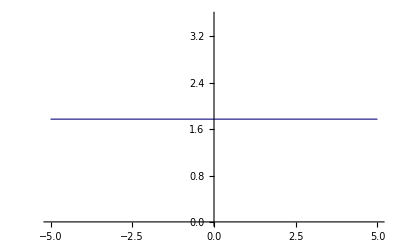

```mathematica
Plot[Evaluate[h[m]],{m,-5,5}]
```

```mathematica
Table[h[x],{x,-1,1,0.1}]
```

{Convolve[0.367879,HeavisideTheta[0.],-1.,-1.],Convolve[0.444858,1,-0.9,-0.9],Convolve[0.527292,1,-0.8,-0.8],Convolve[0.612626,1,-0.7,-0.7],Convolve[0.697676,1,-0.6,-0.6],Convolve[0.778801,1,-0.5,-0.5],Convolve[0.852144,1,-0.4,-0.4],Convolve[0.913931,1,-0.3,-0.3],Convolve[0.960789,1,-0.2,-0.2],Convolve[0.99005,1,-0.1,-0.1],Convolve[1.,1,5.55112×10^-17,5.55112×10^-17],Convolve[0.99005,1,0.1,0.1],Convolve[0.960789,1,0.2,0.2],Convolve[0.913931,1,0.3,0.3],Convolve[0.852144,1,0.4,0.4],Convolve[0.778801,1,0.5,0.5],Convolve[0.697676,1,0.6,0.6],Convolve[0.612626,1,0.7,0.7],Convolve[0.527292,1,0.8,0.8],Convolve[0.444858,1,0.9,0.9],Convolve[0.367879,1,1.,1.]-Convolve[0.367879,HeavisideTheta[0.],1.,1.]}

```mathematica
h[0.]
```

1.49365

```mathematica
h[1.]
```

0.882081

```mathematica
h[0.1]
```

1.4863